```mathematica
(*The number of moment to use*)
nMaxMomentums=40;
(*Aqui im porto la imagen comentarlo*)
imageToSampleOriginal=Import["/home/jesusedel/Descargas/statistical-analysis-01.jpg"];
(*The image is convert to grayscale*)
imageToSample=(*Image[Evaluate[Table[RandomReal[],{j,20},{i,20}]]];*)
ColorConvert[imageToSampleOriginal,"Grayscale"];
(*
 @function: The function constructor that makes a 
cordinate transformation to center of rectangular image
 *)
(*
@param:{Number} the number of pixel*)
(*@return:{Function} a function that calculate the coordinate with origin in center of rectangular image*)
coordinateMapping[N_]:= If[EvenQ[N],N*#/(N-1)(*# is the arg of pure function, #1 the second, etc*)-N(N+1)/(2(N-1)) &(*with & operator build a pure function*),#-(N+1)/2&];

(*
Subscript[R, n]^m= ∑_(k=0)^((n-Abs[m])/2) ((-1)^k(n-k)!)/(k! ((n+m)/2-k)!((n-m)/2-k)!)ρ^(n-2k)
*)
(*@function*)
(*@params:{Number,Number,Number} n,m,ρ*)
(*@return:{Number} R(n,m,ρ)*)
R[n_,m_,ρ_]:=∑_(k=0)^((n-m)/2) (-1)^k Factorial[n-k]/(Factorial[k]*Factorial[(n+m)/2-k]Factorial[(n-m)/2-k])If[ρ≠0,ρ^(n-2k),0];
(*Calculate the θ=ArcTan(y/x)*)
(*@function: θ(x,y)*)
(*@params:{Number,Number}  abscissa coordinate, ordinate coordinate*)
(*@return:{Number} θ angle*)
theta[x_,y_]:=If[
(*if the vector is the right quadrant *)
x> 0,
N[ArcTan[y/x]],
(*if the vector is the left quadrant *)
If[x!=0,N[ArcTan[y/x]],Pi/2]+Pi
];

(*Calculate the ρ=√(x^2+y^2)*)
(*@function: ρ(x,y)*)
(*@params:{Number,Number} abscissa coordinate, ordinate coordinate*)
(*@return:{Number} ρ radial coordinate*)
rho[x_,y_]:=Sqrt[x^2+y^2];
(*Calculate the Subscript[Z, n]^m=Subscript[R, n]^m e^ⅈmθ*)
(*@function: Subscript[Z, n]^m(ρ,θ)*)
(*@params:{Number,Number} radial coordinate, theta coordinate*)
(*@return:{Number} zernik function*)
Z[x_,y_,n_,m_]:=R[n,m,rho[x,y]] Exp[ⅈ m theta[x,y]];
(*define the matrix of pixels*)
(*@matrix*)
pixels =ImageData[imageToSample][[1;;5,1;;5]](*uncoment this part if you want to take only a part of image, this case 50 pixels down-left part[[1;;50,1;;50]]*);
(*get the dimensios of image in pixels*)
imageDimensions=Dimensions[pixels];
(*define the hight pixels*)
max1=imageDimensions[[1]];
(*define the width pixels*)
max2=imageDimensions[[2]];
(*radio of circle*)
rhoCircle =Sqrt[max1^2+max2^2]/4; 
(*transformation from square to circle*)
transformation[points_]:={#[[1]] Sqrt[1-(#[[2]]^2/2)],#[[2]] Sqrt[1-(#[[1]]^2/2)]/rhoCircle}&/@#&/@points;
(*define the function to ontain the x coordinate with the origin in the image rectangular center*)
(*@function*)
x=coordinateMapping[max2];
(*define the function to ontain the y coordinate with the origin in the image rectangular center*)
(*@function*)
y=coordinateMapping[max1];
(*the original coords of image obtained, the center is in left-down corner*)
originalCoords = Table[{j,i},{i,1,max1},{j,1,max2}];
(*map the original coords to one with origin in center of image*)
centeringCoords[points_] :={x[#[[1]]],y[#[[2]]] }&/@#&/@points;
(*max if x coords*)
$xmax = If[EvenQ[max2],max2/2,(max2-1)/2];
(*max if y coords*)
$ymax = If[EvenQ[max1],max1/2,(max1-1)/2];
(*nommalization square to unit square*)
normalizationSquare[points_] :={#[[1]]/$xmax,#[[2]]/$ymax }&/@#&/@points;
(*coords mapped to circle*)
circleCoords = transformation[normalizationSquare[centeringCoords[originalCoords]]];
(*obtain the pixel*)
(*@function*)
(*@params:{Number,Number} abcsise coordinate, ordinate coordinate*)
(*@return:{Number} graylavel value*)
imagePixels[i_,j_]:=pixels[[j,i]];
(*obtain the zernik moments*)
(*@function*)
(*@params:{Number,Number} n, m*)
(*@return:{Number} zernik moment*)
A[n_,m_]:=(n+1)/Pi∑_(i=1)^max1 ∑_(j=1)^max2 If[(circleCoords[[i,j]][[1]])^2+(circleCoords[[i,j]][[2]])^2≤ 1,imagePixels[i,j]Z[circleCoords[[i,j]][[1]],circleCoords[[i,j]][[2]],n,m],0];
(*obtain the first zernik moments*)
(*@function*)
(*@params:{Number} the number of zernik moments to be obtained*)
(*@return:{Matrix} the nxm zernik moments *)

firstNmaxMoments[Nmax_]:=(moments =Table[0,{i,Nmax+1},{j,2 Nmax+1}];
Do[
If[EvenQ[i-j],moments[[i+1,j+i+1]]=A[i,j]]
,{i,0,Nmax},{j,-i,i}];moments);

(*obtain the image reconstructed from the first zernik moments*)
(*@function*)
(*@params:{Number} the number of zernik moments to be used for obtaining the reconstructed image*)
(*@return:{Function} The returned function has as params the x coordiante and y coordinate*)
imagePixelsreconstructed[Nmax_]:=(∑_(i=0)^Nmax ∑_(j=-i)^i firstNmaxMoments[Nmax][[i+1,i+j+1]]Z[#,#1,i,j])&;
(*obtain the image reconstructed using the first moments *)
imagereconstructedFunc = Parallelize[imagePixelsreconstructed[nMaxMomentums]];
(*obtain the matrix of pixels*)
imagereconstructed = Parallelize[Abs[N[imagereconstructedFunc[#[[1]],#[[2]] ]]]&/@#&/@#&[circleCoords]];
(*obtain the image from matrix of pixels*)
imageRec = Image[imagereconstructed,"Byte"];Show[{imageRec,imageToSample}]
(*test of map from square to circle*)
```

Parallelize::nopar1: imagePixelsreconstructed[nMaxMomentums] cannot be parallelized; proceeding with sequential evaluation.

Parallelize::nopar1: (((Abs[N[imagereconstructedFunc[«2»]]]&)/@#1&)/@#1&)[circleCoords] cannot be parallelized; proceeding with sequential evaluation.

```mathematica
Dimensions[ImageData[imageToSample][[1;;12,1;;13]]]
```

{12,13}

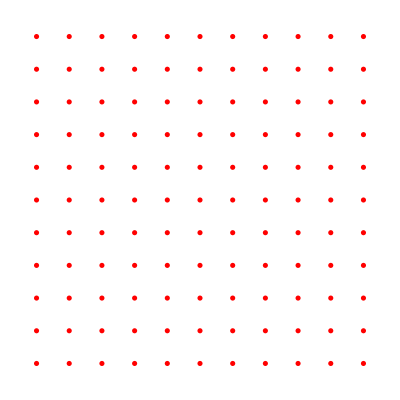

{{-1.,-1.},{-1.,-0.8},{-1.,-0.6},{-1.,-0.4},{-1.,-0.2},{-1.,0.},{-1.,0.2},{-1.,0.4},{-1.,0.6},{-1.,0.8},{-1.,1.}}

{-1.,-1.}

{-1.,-0.8}

{-1.,-0.6}

{-1.,-0.4}

{-1.,-0.2}

{-1.,0.}

{-1.,0.2}

{-1.,0.4}

{-1.,0.6}

{-1.,0.8}

{-1.,1.}

{{-0.8,-1.},{-0.8,-0.8},{-0.8,-0.6},{-0.8,-0.4},{-0.8,-0.2},{-0.8,0.},{-0.8,0.2},{-0.8,0.4},{-0.8,0.6},{-0.8,0.8},{-0.8,1.}}

{-0.8,-1.}

{-0.8,-0.8}

{-0.8,-0.6}

{-0.8,-0.4}

{-0.8,-0.2}

{-0.8,0.}

{-0.8,0.2}

{-0.8,0.4}

{-0.8,0.6}

{-0.8,0.8}

{-0.8,1.}

{{-0.6,-1.},{-0.6,-0.8},{-0.6,-0.6},{-0.6,-0.4},{-0.6,-0.2},{-0.6,0.},{-0.6,0.2},{-0.6,0.4},{-0.6,0.6},{-0.6,0.8},{-0.6,1.}}

{-0.6,-1.}

{-0.6,-0.8}

{-0.6,-0.6}

{-0.6,-0.4}

{-0.6,-0.2}

{-0.6,0.}

{-0.6,0.2}

{-0.6,0.4}

{-0.6,0.6}

{-0.6,0.8}

{-0.6,1.}

{{-0.4,-1.},{-0.4,-0.8},{-0.4,-0.6},{-0.4,-0.4},{-0.4,-0.2},{-0.4,0.},{-0.4,0.2},{-0.4,0.4},{-0.4,0.6},{-0.4,0.8},{-0.4,1.}}

{-0.4,-1.}

{-0.4,-0.8}

{-0.4,-0.6}

{-0.4,-0.4}

{-0.4,-0.2}

{-0.4,0.}

{-0.4,0.2}

{-0.4,0.4}

{-0.4,0.6}

{-0.4,0.8}

{-0.4,1.}

{{-0.2,-1.},{-0.2,-0.8},{-0.2,-0.6},{-0.2,-0.4},{-0.2,-0.2},{-0.2,0.},{-0.2,0.2},{-0.2,0.4},{-0.2,0.6},{-0.2,0.8},{-0.2,1.}}

{-0.2,-1.}

{-0.2,-0.8}

{-0.2,-0.6}

{-0.2,-0.4}

{-0.2,-0.2}

{-0.2,0.}

{-0.2,0.2}

{-0.2,0.4}

{-0.2,0.6}

{-0.2,0.8}

{-0.2,1.}

{{0.,-1.},{0.,-0.8},{0.,-0.6},{0.,-0.4},{0.,-0.2},{0.,0.},{0.,0.2},{0.,0.4},{0.,0.6},{0.,0.8},{0.,1.}}

{0.,-1.}

{0.,-0.8}

{0.,-0.6}

{0.,-0.4}

{0.,-0.2}

{0.,0.}

{0.,0.2}

{0.,0.4}

{0.,0.6}

{0.,0.8}

{0.,1.}

{{0.2,-1.},{0.2,-0.8},{0.2,-0.6},{0.2,-0.4},{0.2,-0.2},{0.2,0.},{0.2,0.2},{0.2,0.4},{0.2,0.6},{0.2,0.8},{0.2,1.}}

{0.2,-1.}

{0.2,-0.8}

{0.2,-0.6}

{0.2,-0.4}

{0.2,-0.2}

{0.2,0.}

{0.2,0.2}

{0.2,0.4}

{0.2,0.6}

{0.2,0.8}

{0.2,1.}

{{0.4,-1.},{0.4,-0.8},{0.4,-0.6},{0.4,-0.4},{0.4,-0.2},{0.4,0.},{0.4,0.2},{0.4,0.4},{0.4,0.6},{0.4,0.8},{0.4,1.}}

{0.4,-1.}

{0.4,-0.8}

{0.4,-0.6}

{0.4,-0.4}

{0.4,-0.2}

{0.4,0.}

{0.4,0.2}

{0.4,0.4}

{0.4,0.6}

{0.4,0.8}

{0.4,1.}

{{0.6,-1.},{0.6,-0.8},{0.6,-0.6},{0.6,-0.4},{0.6,-0.2},{0.6,0.},{0.6,0.2},{0.6,0.4},{0.6,0.6},{0.6,0.8},{0.6,1.}}

{0.6,-1.}

{0.6,-0.8}

{0.6,-0.6}

{0.6,-0.4}

{0.6,-0.2}

{0.6,0.}

{0.6,0.2}

{0.6,0.4}

{0.6,0.6}

{0.6,0.8}

{0.6,1.}

{{0.8,-1.},{0.8,-0.8},{0.8,-0.6},{0.8,-0.4},{0.8,-0.2},{0.8,0.},{0.8,0.2},{0.8,0.4},{0.8,0.6},{0.8,0.8},{0.8,1.}}

{0.8,-1.}

{0.8,-0.8}

{0.8,-0.6}

{0.8,-0.4}

{0.8,-0.2}

{0.8,0.}

{0.8,0.2}

{0.8,0.4}

{0.8,0.6}

{0.8,0.8}

{0.8,1.}

{{1.,-1.},{1.,-0.8},{1.,-0.6},{1.,-0.4},{1.,-0.2},{1.,0.},{1.,0.2},{1.,0.4},{1.,0.6},{1.,0.8},{1.,1.}}

{1.,-1.}

{1.,-0.8}

{1.,-0.6}

{1.,-0.4}

{1.,-0.2}

{1.,0.}

{1.,0.2}

{1.,0.4}

{1.,0.6}

{1.,0.8}

{1.,1.}

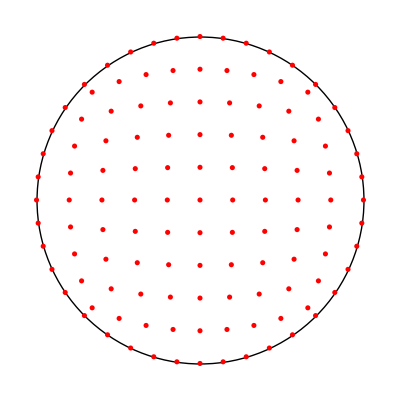

```mathematica
transformation[points_]:=(Print[#];{#[[1]] Sqrt[1-(#[[2]]^2/2)],#[[2]] Sqrt[1-(#[[1]]^2/2)]})&/@(Print[#];#)&/@points;
points=Table[{a,b},{a,-1,1,0.2},{b,-1,1,0.2}];

Show[Graphics[{EdgeForm[Thick],White,Rectangle[{-1,-1},{1,1}]}],ListPlot[Flatten[points,1],AspectRatio->1,PlotStyle->Red]]
Show[Graphics[{Thick,Circle[]}],ListPlot[Flatten[transformation[points],1],AspectRatio->1,PlotStyle->Red]]
```

```mathematica
a = transformation[points]
```

{{-1.,-1.},{-1.,-0.8},{-1.,-0.6},{-1.,-0.4},{-1.,-0.2},{-1.,0.},{-1.,0.2},{-1.,0.4},{-1.,0.6},{-1.,0.8},{-1.,1.}}

{-1.,-1.}

{-1.,-0.8}

{-1.,-0.6}

{-1.,-0.4}

{-1.,-0.2}

{-1.,0.}

{-1.,0.2}

{-1.,0.4}

{-1.,0.6}

{-1.,0.8}

{-1.,1.}

{{-0.8,-1.},{-0.8,-0.8},{-0.8,-0.6},{-0.8,-0.4},{-0.8,-0.2},{-0.8,0.},{-0.8,0.2},{-0.8,0.4},{-0.8,0.6},{-0.8,0.8},{-0.8,1.}}

{-0.8,-1.}

{-0.8,-0.8}

{-0.8,-0.6}

{-0.8,-0.4}

{-0.8,-0.2}

{-0.8,0.}

{-0.8,0.2}

{-0.8,0.4}

{-0.8,0.6}

{-0.8,0.8}

{-0.8,1.}

{{-0.6,-1.},{-0.6,-0.8},{-0.6,-0.6},{-0.6,-0.4},{-0.6,-0.2},{-0.6,0.},{-0.6,0.2},{-0.6,0.4},{-0.6,0.6},{-0.6,0.8},{-0.6,1.}}

{-0.6,-1.}

{-0.6,-0.8}

{-0.6,-0.6}

{-0.6,-0.4}

{-0.6,-0.2}

{-0.6,0.}

{-0.6,0.2}

{-0.6,0.4}

{-0.6,0.6}

{-0.6,0.8}

{-0.6,1.}

{{-0.4,-1.},{-0.4,-0.8},{-0.4,-0.6},{-0.4,-0.4},{-0.4,-0.2},{-0.4,0.},{-0.4,0.2},{-0.4,0.4},{-0.4,0.6},{-0.4,0.8},{-0.4,1.}}

{-0.4,-1.}

{-0.4,-0.8}

{-0.4,-0.6}

{-0.4,-0.4}

{-0.4,-0.2}

{-0.4,0.}

{-0.4,0.2}

{-0.4,0.4}

{-0.4,0.6}

{-0.4,0.8}

{-0.4,1.}

{{-0.2,-1.},{-0.2,-0.8},{-0.2,-0.6},{-0.2,-0.4},{-0.2,-0.2},{-0.2,0.},{-0.2,0.2},{-0.2,0.4},{-0.2,0.6},{-0.2,0.8},{-0.2,1.}}

{-0.2,-1.}

{-0.2,-0.8}

{-0.2,-0.6}

{-0.2,-0.4}

{-0.2,-0.2}

{-0.2,0.}

{-0.2,0.2}

{-0.2,0.4}

{-0.2,0.6}

{-0.2,0.8}

{-0.2,1.}

{{0.,-1.},{0.,-0.8},{0.,-0.6},{0.,-0.4},{0.,-0.2},{0.,0.},{0.,0.2},{0.,0.4},{0.,0.6},{0.,0.8},{0.,1.}}

{0.,-1.}

{0.,-0.8}

{0.,-0.6}

{0.,-0.4}

{0.,-0.2}

{0.,0.}

{0.,0.2}

{0.,0.4}

{0.,0.6}

{0.,0.8}

{0.,1.}

{{0.2,-1.},{0.2,-0.8},{0.2,-0.6},{0.2,-0.4},{0.2,-0.2},{0.2,0.},{0.2,0.2},{0.2,0.4},{0.2,0.6},{0.2,0.8},{0.2,1.}}

{0.2,-1.}

{0.2,-0.8}

{0.2,-0.6}

{0.2,-0.4}

{0.2,-0.2}

{0.2,0.}

{0.2,0.2}

{0.2,0.4}

{0.2,0.6}

{0.2,0.8}

{0.2,1.}

{{0.4,-1.},{0.4,-0.8},{0.4,-0.6},{0.4,-0.4},{0.4,-0.2},{0.4,0.},{0.4,0.2},{0.4,0.4},{0.4,0.6},{0.4,0.8},{0.4,1.}}

{0.4,-1.}

{0.4,-0.8}

{0.4,-0.6}

{0.4,-0.4}

{0.4,-0.2}

{0.4,0.}

{0.4,0.2}

{0.4,0.4}

{0.4,0.6}

{0.4,0.8}

{0.4,1.}

{{0.6,-1.},{0.6,-0.8},{0.6,-0.6},{0.6,-0.4},{0.6,-0.2},{0.6,0.},{0.6,0.2},{0.6,0.4},{0.6,0.6},{0.6,0.8},{0.6,1.}}

{0.6,-1.}

{0.6,-0.8}

{0.6,-0.6}

{0.6,-0.4}

{0.6,-0.2}

{0.6,0.}

{0.6,0.2}

{0.6,0.4}

{0.6,0.6}

{0.6,0.8}

{0.6,1.}

{{0.8,-1.},{0.8,-0.8},{0.8,-0.6},{0.8,-0.4},{0.8,-0.2},{0.8,0.},{0.8,0.2},{0.8,0.4},{0.8,0.6},{0.8,0.8},{0.8,1.}}

{0.8,-1.}

{0.8,-0.8}

{0.8,-0.6}

{0.8,-0.4}

{0.8,-0.2}

{0.8,0.}

{0.8,0.2}

{0.8,0.4}

{0.8,0.6}

{0.8,0.8}

{0.8,1.}

{{1.,-1.},{1.,-0.8},{1.,-0.6},{1.,-0.4},{1.,-0.2},{1.,0.},{1.,0.2},{1.,0.4},{1.,0.6},{1.,0.8},{1.,1.}}

{1.,-1.}

{1.,-0.8}

{1.,-0.6}

{1.,-0.4}

{1.,-0.2}

{1.,0.}

{1.,0.2}

{1.,0.4}

{1.,0.6}

{1.,0.8}

{1.,1.}

{{{-0.707107,-0.707107},{-0.824621,-0.565685},{-0.905539,-0.424264},{-0.959166,-0.282843},{-0.989949,-0.141421},{-1.,0.},{-0.989949,0.141421},{-0.959166,0.282843},{-0.905539,0.424264},{-0.824621,0.565685},{-0.707107,0.707107}},{{-0.565685,-0.824621},{-0.659697,-0.659697},{-0.724431,-0.494773},{-0.767333,-0.329848},{-0.79196,-0.164924},{-0.8,0.},{-0.79196,0.164924},{-0.767333,0.329848},{-0.724431,0.494773},{-0.659697,0.659697},{-0.565685,0.824621}},{{-0.424264,-0.905539},{-0.494773,-0.724431},{-0.543323,-0.543323},{-0.5755,-0.362215},{-0.59397,-0.181108},{-0.6,0.},{-0.59397,0.181108},{-0.5755,0.362215},{-0.543323,0.543323},{-0.494773,0.724431},{-0.424264,0.905539}},{{-0.282843,-0.959166},{-0.329848,-0.767333},{-0.362215,-0.5755},{-0.383667,-0.383667},{-0.39598,-0.191833},{-0.4,0.},{-0.39598,0.191833},{-0.383667,0.383667},{-0.362215,0.5755},{-0.329848,0.767333},{-0.282843,0.959166}},{{-0.141421,-0.989949},{-0.164924,-0.79196},{-0.181108,-0.59397},{-0.191833,-0.39598},{-0.19799,-0.19799},{-0.2,0.},{-0.19799,0.19799},{-0.191833,0.39598},{-0.181108,0.59397},{-0.164924,0.79196},{-0.141421,0.989949}},{{0.,-1.},{0.,-0.8},{0.,-0.6},{0.,-0.4},{0.,-0.2},{0.,0.},{0.,0.2},{0.,0.4},{0.,0.6},{0.,0.8},{0.,1.}},{{0.141421,-0.989949},{0.164924,-0.79196},{0.181108,-0.59397},{0.191833,-0.39598},{0.19799,-0.19799},{0.2,0.},{0.19799,0.19799},{0.191833,0.39598},{0.181108,0.59397},{0.164924,0.79196},{0.141421,0.989949}},{{0.282843,-0.959166},{0.329848,-0.767333},{0.362215,-0.5755},{0.383667,-0.383667},{0.39598,-0.191833},{0.4,0.},{0.39598,0.191833},{0.383667,0.383667},{0.362215,0.5755},{0.329848,0.767333},{0.282843,0.959166}},{{0.424264,-0.905539},{0.494773,-0.724431},{0.543323,-0.543323},{0.5755,-0.362215},{0.59397,-0.181108},{0.6,0.},{0.59397,0.181108},{0.5755,0.362215},{0.543323,0.543323},{0.494773,0.724431},{0.424264,0.905539}},{{0.565685,-0.824621},{0.659697,-0.659697},{0.724431,-0.494773},{0.767333,-0.329848},{0.79196,-0.164924},{0.8,0.},{0.79196,0.164924},{0.767333,0.329848},{0.724431,0.494773},{0.659697,0.659697},{0.565685,0.824621}},{{0.707107,-0.707107},{0.824621,-0.565685},{0.905539,-0.424264},{0.959166,-0.282843},{0.989949,-0.141421},{1.,0.},{0.989949,0.141421},{0.959166,0.282843},{0.905539,0.424264},{0.824621,0.565685},{0.707107,0.707107}}}

```mathematica
a[[1,1]]
```

{-0.707107,-0.707107}